# Homework 4

## Wang Long 1101110160

Mathematica 8.01

## Parameters

```mathematica
a0=1;
h0=0.7;
ΩΛ0=0.75;
Ωm0=0.25;
Ωr0=0;
Ωk0=0;
Kc=0;
c=3*^5km/s;
```

## Function

### Hubble time H^-1, lookback time t

```mathematica
H0=h0*100 km s^-1 Mpc^-1;
a[z_]:=a0/(1+z)
HLCDM[z_]:=H0 √(ΩΛ0+Ωm0/a[z]^3+Ωr0/a[z]^4+Ωk0/a[z]^2)
tLCDM[z_]:=NIntegrate[1/((1+zn)*HLCDM[zn])/.{Mpc->3.08567756*^19 km,s->1/(1*^9*365*24*3600)},{zn,0,z}]Gyr
tHLCDM[z_]:=1/HLCDM[z]/.{Mpc->3.08567756*^19 km,s->1/(1*^9*365*24*3600)Gyr}
```

### Cosmic Distances

```mathematica
Sinn[x_,k_Integer/;-1≤k≤1]:=Piecewise[{{Sin[x],k==1},{x,k==0},{Sinh[x],k==-1}}]
dc[z_]:=NIntegrate[c/HLCDM[zn]/Mpc/.{km-> 1/3.08567756*^19 Mpc},{zn,0,z}]Mpc
dA[z_]:=a[z]*Sinn[dc[z]/Mpc,Kc]Mpc
dL[z_]:=(1+z)Sinn[dc[z]/Mpc,Kc]Mpc
```

### Distance moduli μ

```mathematica
Kcorrection[z_,n_]:=2.5(n-1)Log10[1+z]mag
μmagk[m_,M_,A_,z_,n_]:=m-M-Kcorrection[z,n]-A
μzk[z_]:=(5Log10[dL[z]/Mpc]+25)mag
μmag[m_.M_,A_]:=m-M-A
μz[z_,n_]:=(5Log10[dL[z]/Mpc]+25)mag+Kcorrection[z,n]
```

## Calculation and Plot

```mathematica
Needs["PlotLegends`"]
Off[NIntegrate::nlim]
Off[General::stop]
Off[NIntegrate::slwcon]
Off[NIntegrate::ncvb]
```

### Hubble time H^-1 & lookback time t

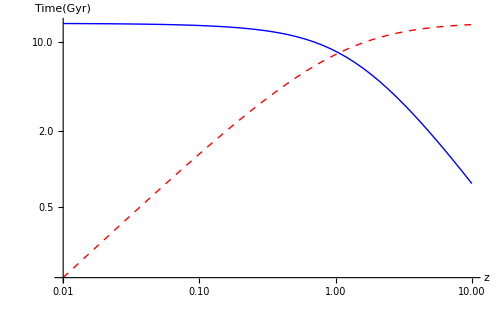

```mathematica
LogLogPlot[{tHLCDM[z]/Gyr,tLCDM[z]/Gyr},{z,0.01,10},PlotStyle->{Blue,{Red,Dashed,Thick}},AxesLabel->{"z","Time(Gyr)"},PlotLegend->{"H^-1","t"},LegendPosition->{1,0},LegendSize->{0.3,0.2},LegendShadow->None,ImageSize->500]
```

### Comoving, angular diameter and luminosity distance

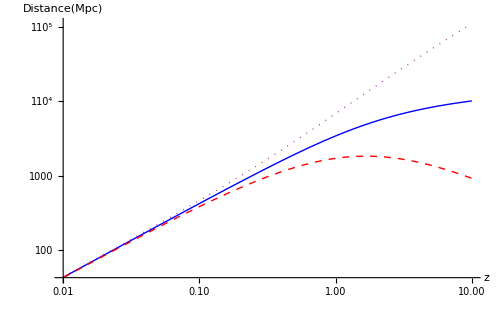

```mathematica
LogLogPlot[{dc[z]/Mpc,dA[z]/Mpc,dL[z]/Mpc},{z,0.01,10},PlotStyle->{Blue,{Red,Dashed,Thick},{Purple,Dotted,Thick}},AxesLabel->{"z","Distance(Mpc)"},PlotLegend->{"comoving","angular diameter","luminosity distances"},LegendPosition->{1,0},LegendSize->{0.7,0.2},LegendShadow->None,ImageSize->500]
```

### distance moduli μ

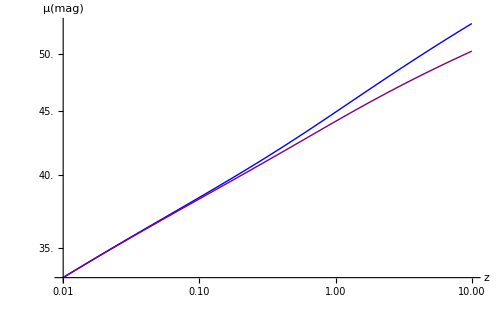

```mathematica
LogLogPlot[{μz[z,2]/mag,μzk[z]/mag},{z,0.01,10},PlotStyle->{Blue,{Purple,Thick}},AxesLabel->{"z","μ(mag)"},PlotLegend->{"μ(no k-correction)","μ(k-correction)"},LegendPosition->{1,0},LegendSize->{0.65,0.2},LegendShadow->None,ImageSize->500]
```